## Monolayer, Isotropic Forces

```mathematica
ClearAll[ex, ey, n, latticepts,unitcellpts,dcutoff,bonds,segmentn,segments,qloop, freqs,D3x3]
```

## Layer Parameters

```mathematica
ex={1,0,0};
ey={0,1,0};
```

## Create Lattice and unit cell

```mathematica
n=50;

latticepts={};
unitcellpts={{0,0,0}};
For[i=-n/2,i<=n/2,i++,
For[j=-n/2,j<=n/2,j++,
AppendTo[latticepts, i*ex+j*ey];
]
]
ListPointPlot3D[latticepts]
```

-Graphics3D-

## Create List of Bonds Included

```mathematica
dcutoff=2;
bonds={};
bondgraphics={};
unitcells={-ex-ey,-ex,-ex+ey,-ey,{0,0,0},ey,ex-ey,ex,ex+ey};
Monitor[For[i=1,i<=Length[unitcellpts],i++,
For[j=1,j<=Length[unitcellpts],j++,
For[R=1,R<=Length[unitcells],R++,
d=Norm[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]];
If[d!=0&&d<=dcutoff,
dhat=1/d*(unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]);
AppendTo[bonds,{i, j,R,dhat,d}];
AppendTo[bondgraphics,Line[{unitcellpts[[i]],unitcellpts[[j]]+unitcells[[R]]}]];
];
]
]
],{i,j}]
Show[Graphics3D[bondgraphics],ListPointPlot3D[unitcellpts]]
```

-Graphics3D-

## Create Momentum Loop

```mathematica
segmentn=30;
segments={{0,0,0},{π,0,0},{π,π,0},{0,0,0}};
qloop={};
For[s=1,s<Length[segments],s++,
For[i=1,i<=segmentn,i++,
AppendTo[qloop,segments[[s]]+i*((segments[[s+1]]-segments[[s]])/segmentn)]
]
]
ListPointPlot3D[qloop]
```

-Graphics3D-

## Main Loop

```mathematica
freqs={};
λ=10;
Monitor[For[k=1,k<=Length[qloop],k++,
(*Momentum*)
q=qloop[[k]]; 
(*Dynamics Matrixes*)
DynamicsMatrix=ConstantArray[0,{3*Length[unitcellpts],3*Length[unitcellpts]}];
(*Loop over bonds*)
For[i=1,i<=Length[bonds],i++,
a1=bonds[[i]][[1]];
a2=bonds[[i]][[2]];
R=bonds[[i]][[3]];
dhat=bonds[[i]][[4]];
d=bonds[[i]][[5]];
D3x3=ⅇ^(-λ*d){{1,0,0},{0,1,0},{0,0,1}};
DynamicsMatrix[[3a1-2;;3a1,3a1-2;;3a1]]+=-1*D3x3;
DynamicsMatrix[[3a1-2;;3a1,3a2-2;;3a2]]+=D3x3*ⅇ^(I*unitcells[[R]].q);
];
AppendTo[freqs,√(-Eigenvalues[DynamicsMatrix])]
]
,{a1,a2,k,D3x3}]
```

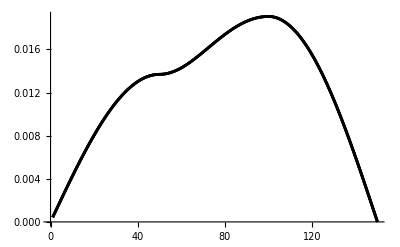

```mathematica
Show[ListLinePlot[Table[freqs[[;;,i]],{i,1,3*Length[unitcellpts]}],PlotStyle->{{Black}}]]
```

## Analytic Results

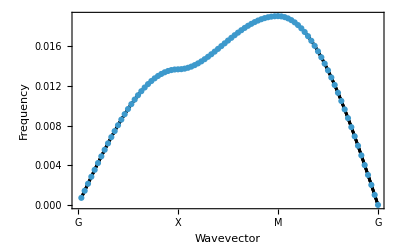

```mathematica
DM[qx_,qy_,k1_,k2_]:=({{4*k1*(Sin[1/2 qx]^2+Sin[1/2 qy]^2)+k2*(4-4Cos[qx]Cos[qy]), 0}, {0, 4*k1*(Sin[1/2 qx]^2+Sin[1/2 qy]^2)+k2*(4-4Cos[qx]Cos[qy])}})
Show[ListLinePlot[Table[freqs[[;;,i]],{i,1,3*Length[unitcellpts]}],PlotStyle->{{Black}}],ListPlot[Table[√Eigenvalues[DM[qloop[[k]][[1]],qloop[[k]][[2]],ⅇ^(-λ*1),ⅇ^(-λ*√2)]][[1]],{k,1,Length[qloop]}]],Frame->True,FrameTicks->{{Automatic,None},{{{0,"G"},{segmentn,"X"},{2*segmentn,"M"},{3*segmentn,"G"}},None}},FrameLabel->{{"Frequency",""},{"Wavevector", ""}}]
```